# Monte Carlo

## The Sum of 12 Uniform Random Variables

In Monte Carlo option pricing, one needs to generate standard normal random variables. 
Perhaps the simplest way to do this is to use the sum of 12 uniform variables. 
Here are the plots and the probability density functions of the sums of uniform random variables.

### The Sum of 1, 2, and 3 Uniform Variables

Piecewise[{{1, 0≤x≤1}, {0, True}}]

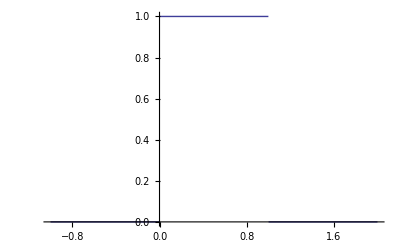

```mathematica
𝒰=UniformDistribution[{0, 1}];
h[x_]:=PDF[𝒰, x];
h[x]
Plot[h[x], {x, -1, 2}, PlotRange->All]
```

Piecewise[{{0, x<0}, {x, 0≤x<1}, {2-x, 1≤x≤2}, {0, True}}]

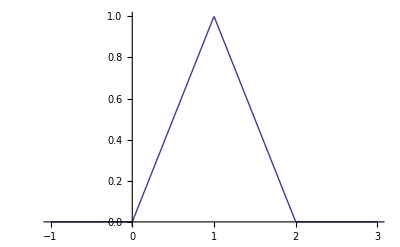

```mathematica
bb=TransformedDistribution[a1+a2, {a1\[Distributed]𝒰, a2\[Distributed]𝒰}];
h[x_]:=PDF[bb, x];
h[x]
Plot[h[x], {x, -1, 3}, PlotRange->All]
```

Piecewise[{{0, x<0}, {x^2/2, 0≤x<1}, {1/2 (-3 (-1+x)^2+x^2), 1≤x<2}, {1/2 (3-x)^2, 2≤x≤3}, {0, True}}]

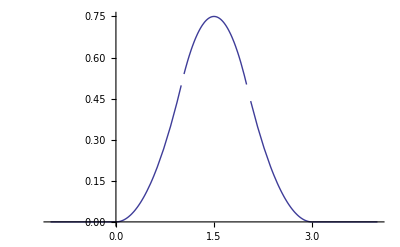

```mathematica
bb=TransformedDistribution[a1+a2+a3, {a1\[Distributed]𝒰, a2\[Distributed]𝒰, a3\[Distributed]𝒰}];
h[x_]:=PDF[bb, x];
h[x]
Plot[h[x], {x, -1, 4}, PlotRange->All]
```

### The Sum of 12 Uniform Variables

The first figure shows the plot of a standard normal random variable (red line) and that of the sum of 12 uniform variables (blue line). 
The second one shows their difference.

Piecewise[{{0, x<0}, {x^11/39916800, 0≤x<1}, {(-12 (-1+x)^11+x^11)/39916800, 1≤x<2}, {(66 (-2+x)^11-12 (-1+x)^11+x^11)/39916800, 2≤x<3}, {(-220 (-3+x)^11+66 (-2+x)^11-12 (-1+x)^11+x^11)/39916800, 3≤x<4}, {(495 (-4+x)^11-220 (-3+x)^11+66 (-2+x)^11-12 (-1+x)^11+x^11)/39916800, 4≤x<5}, {(-792 (-5+x)^11+495 (-4+x)^11-220 (-3+x)^11+66 (-2+x)^11-12 (-1+x)^11+x^11)/39916800, 5≤x<6}, {(-792 (7-x)^11+495 (8-x)^11-220 (9-x)^11+66 (10-x)^11-12 (11-x)^11+(12-x)^11)/39916800, 6≤x<7}, {(495 (8-x)^11-220 (9-x)^11+66 (10-x)^11-12 (11-x)^11+(12-x)^11)/39916800, 7≤x<8}, {(-220 (9-x)^11+66 (10-x)^11-12 (11-x)^11+(12-x)^11)/39916800, 8≤x<9}, {(66 (10-x)^11-12 (11-x)^11+(12-x)^11)/39916800, 9≤x<10}, {(-12 (11-x)^11+(12-x)^11)/39916800, 10≤x<11}, {(12-x)^11/39916800, 11≤x≤12}, {0, True}}]

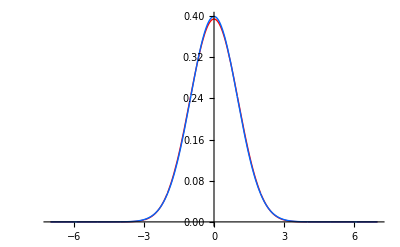

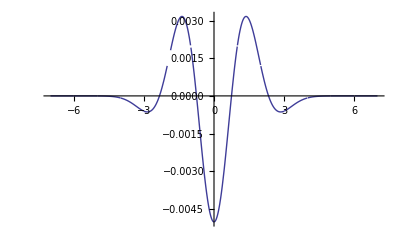

```mathematica
dd=TransformedDistribution[a1+a2+a3+a4+a5+a6+a7+a8+a9+a10+a11+a12, {a1\[Distributed]𝒰, a2\[Distributed]𝒰, a3\[Distributed]𝒰,a4\[Distributed]𝒰, a5\[Distributed]𝒰, a6\[Distributed]𝒰, a7\[Distributed]𝒰, a8\[Distributed]𝒰, a9\[Distributed]𝒰, a10\[Distributed]𝒰, a11\[Distributed]𝒰, a12\[Distributed]𝒰}];

f[x_]:=PDF[dd,x];
g[x_]:=f[x+6];
f[x]
Plot[{g[x],1/(√(2π))ⅇ^(-x^2/2)}, {x, -7, 7}, PlotRange->All, PlotStyle->{Hue[0], Hue[.6]}]
Plot[g[x]-1/(√(2π))ⅇ^(-x^2/2), {x, -7, 7}, PlotRange->All]
```

### Box-Muller

According to the Box-Muller algorithm, the random variable √(-2log U_1)cos(2π U_2) are normally distributed, where U_1, U_2 are uniform random variable. 
But Mathematica fails to work out the distribution of √(-2log U_1)cos(2π U_2).

```mathematica
bb=TransformedDistribution[√(-2Log[a1])Cos[2π a2], {a1\[Distributed]𝒰, a2\[Distributed]𝒰}];
h[x_]:=PDF[bb, x];
h[x]
```

$Aborted

## Modified Box-Muller Algorithm

### The Idea

11/25/2010

In the Box-Muller algorithm, two uniform random variables are first generated to obtain two iid standard normal random variables. 
The two uniform variables should satisfy some specific condition,
or otherwise they will be thrown away and another two uniform variables are generated. 
When every two uniform variables are generated, they have 1-π/4=21.46% chance of being thrown away. 
Here some of the uniform variables that are thrown away are kept and used to generate normal random variables, 
in order to make the Box-Muller Algorithm more efficient.

```mathematica
Show[Graphics[{
Circle[{0,0},1], 

Circle[{-1,-1},√2-1, {0, π/2}], 
Circle[{1,-1},√2-1, {π/2, π}], 
Circle[{1,1},√2-1, {π, (3π)/2}], 
Circle[{-1,1},√2-1, {(3π)/2, 2π}], 
Line[{{1, 1}, {-1, 1}, {-1, -1}, {1, -1}, {1, 1}}]
},AspectRatio-> 1,Axes-> Automatic, ImageSize->300]];
```

```mathematica
2(π/4)+NSum[2i(1-π/4)^(i-1), {i,2, ∞}](* how many uniform variables are needed to generate two normal variables on average in the Box-Muller algorithm? *)
2(((4-2 √2)π)/4)+NSum[2i(1-((4-2 √2)π)/4)^(i-1), {i,2, ∞}](* how many uniform variables are needed in our algorithm? *)
```

2.81307

2.20247

```mathematica
Show[Graphics[{
Circle[{√3,1},√3, {π, (7π)/6}], 
Circle[{0,0},√3, {0, π/6}], 
Line[{{0, 0}, {√3, 0}, {√3, 1}, {0, 1}, {0, 0}, {√3, 1}}]
},AspectRatio-> 1/√3,Axes-> Automatic, ImageSize->300]];
```

```mathematica
(* 
Another way to make the chance of being thrown away smaller,  
but it takes more uniform variables to generate normal variables. 
*)
n=6;
3((π/(2n))/(Tan[π/n]/2))+NSum[3i(1-(π/(2n))/(Tan[π/n]/2))^(i-1), {i,2, ∞}]
```

3.36826

```mathematica
n=72;
3((π/(2n))/(Tan[π/n]/2))+NSum[3i(1-(π/(2n))/(Tan[π/n]/2))^(i-1), {i,2, ∞}]
```

3.00191

### Normal Random Variable Generator

11/29/2010

Based on the above idea

```mathematica
NormGen[]:=Block[{u1, u2, x, y, s, w, z, t}, 
While[True, 
u1=Random[];
u2=Random[];

x=2u1-1;
y=2u2-1;
If[(s=x^2+y^2)<1, Return[√((-2Log[s])/s){x, y}]];
w=Abs[x]-1;
z=Abs[y]-1;
If[(t=w^2+z^2)<3-2 √2, Return[√((-2Log[t/(3-2 √2)])/t){Sign[x]w, Sign[y]z}]];
];
];

Show[Graphics[Point/@Table[NormGen[], {10000}],AspectRatio->Automatic]];
```

## Random Walk

### Random Walk M_t

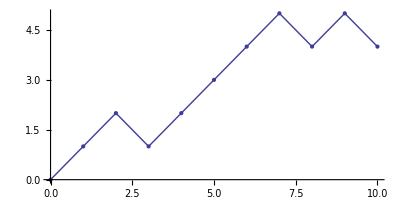

```mathematica
n=10;

ListLinePlot[
Prepend[
{Range[n], (2 RandomInteger[{0, 1}, n]-1)//Accumulate}//Transpose, 
{0, 0}]
, PlotRange->All, PlotStyle->PointSize[Large],Mesh->All, AspectRatio->Automatic]
```

### de Moivre–Laplace theorem

```mathematica
Animate[
DiscretePlot[PDF[BinomialDistribution[n,1/2], x], {x, 0, n}, PlotRange->All,PlotMarkers->Automatic]
, {n, 2^Range[8]},AnimationRunning->False]
```

### Scaled Random Walk 1/(√n)M_(n t)

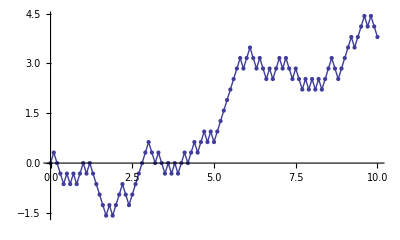

```mathematica
n=100;
r=10;

ListLinePlot[
Prepend[
{Range[n]/r, ((2 RandomInteger[{0, 1}, n]-1)//Accumulate)/(√r)}//Transpose, 
{0, 0}]
, PlotRange->All, PlotStyle->PointSize[Medium],Mesh->All, AspectRatio->Automatic]
```

## Monte Carlo Vanilla Option Pricing

Vanilla options are not path dependent, but here the sample path is generated to
1. plot the figure
2. make it easier to modify this code for path dependent option pricing

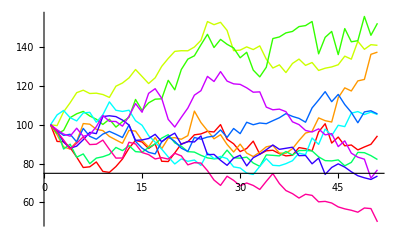

8.50744

18.3049

57.127

```mathematica
T=1;
n=50;(* number of periods *)
p=5000;(* number of paths *)

dt=T/n;

r=0.1;
s=0.3;
s0=100;
K=120;

tmp={};
fig={};

CPUtime=TimeUsed[];
Do[
z=NormalDistribution[0, 1];
aaa=Join[{0}, RandomReal[z, n]//Accumulate];
aaa=s0 Exp[(r-s^2/2)Range[0, T, dt]+s √dt aaa];

AppendTo[tmp, ⅇ^(-r T)Max[(aaa//Last)-K, 0]];
AppendTo[fig, ListLinePlot[aaa, PlotRange->All, PlotStyle->{Hue[i/p]}]]
, {i, p}];

(* some sample price process *)
fig[[Range[1, p, p/10]]]//Show

(* sample mean (option price), sample sd, and running time *)
tmp//Mean  
tmp//StandardDeviation 
TimeUsed[]-CPUtime
```

## Monte Carlo Asian Option Pricing

With control variates method, the sample variance is reduced significantly, and hence the prcing result is better. 
Note that the exact value under this numerical setting this 2.3682854518288..., which is obtained by convolution pricing. 
It does take more time to evaluate the geometric mean of sample prices, but it’s worthy.

### Without Control Variates method

2.43815

6.8015

1.279

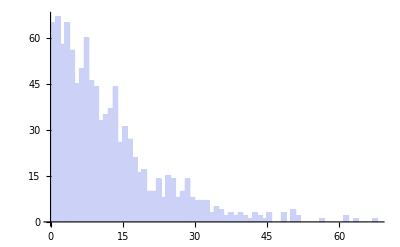

```mathematica
T=1;
n=50;(* number of periods *)
p=5000;(* number of paths *)

dt=T/n;

r=0.1;
s=0.3;
s0=100;
K=120;

tmp={};
fig={};

CPUtime=TimeUsed[];
Do[
z=NormalDistribution[0, 1];
aaa=Join[{0}, RandomReal[z, n]//Accumulate];
aaa=s0 Exp[(r-s^2/2)Range[0, T, dt]+s √dt aaa];
AppendTo[tmp, ⅇ^(-r T)Max[Mean[aaa]-K, 0]];
, {i, p}];

(* sample mean (option price), sample sd, and running time *)
tmp//Mean  
tmp//StandardDeviation 
TimeUsed[]-CPUtime 

(* histogram of sample prices that are not zero *)
Histogram[DeleteCases[tmp//Chop, 0], {1}]
```

### With Control Variates method

2.34895

0.820452

4.462

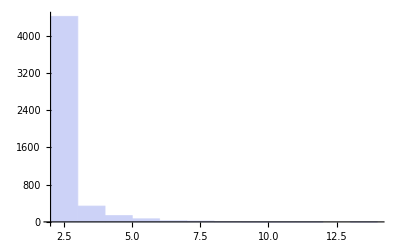

```mathematica
T=1;
n=50;(* number of periods *)
p=5000;(* number of paths *)

dt=T/n;


r=0.1;
s=0.3;
s0=100;
K=120;
Ncdf[x_]:=(1+Erf[x/(√2)])/2;

tmp={};
fig={};

CPUtime=TimeUsed[];
Do[
z=NormalDistribution[0, 1];
aaa=Join[{0}, RandomReal[z, n]//Accumulate];
aaa=s0 Exp[(r-s^2/2)Range[0, T, dt]+s √dt aaa];
(* Sample arithmetic - Sample geometric + Exact geometric*)
AppendTo[tmp, ⅇ^(-r T)Max[Mean[aaa]-K, 0]-ⅇ^(-r T)Max[GeometricMean[aaa]-K, 0]+(s0 ⅇ^(-(r+(n+2)/(6(n+1))s^2)T/2)Ncdf[(Log[s0/K]+(r+(n-1)/(6(n+1))s^2)T/2)/(√((2n+1)/(6(n+1)))s √T)]-K ⅇ^(-r T)Ncdf[(Log[s0/K]+(r-s^2/2)T/2)/(√((2n+1)/(6(n+1)))s √T)])]
, {i, p}];

(* sample mean (option price), sample sd, and running time *)
tmp//Mean  
tmp//StandardDeviation 
TimeUsed[]-CPUtime 

(* histogram of sample prices that are not zero *)
Histogram[DeleteCases[tmp//Chop, 0], {1}]
```